# Zadanie 1

-1/2+2 ⅇ^-x x^2

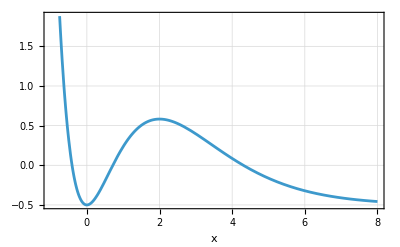

```mathematica
f[x_]=-1/2+2 x^2 ⅇ^-x
wykres=Plot[f[x],{x,-1,8},AxesLabel->Automatic,GridLines->Automatic,Frame->True]
```

```mathematica
sol= {x,0}/.NSolve[f[x]==0,x,Reals]
```

{{-0.407777,0},{0.714806,0},{4.30658,0}}

```mathematica
extr= {x,f[x]}/.Solve[D[f[x],x]==0,x,Reals]
```

{{0,-1/2},{2,-1/2+8/ⅇ^2}}

{{0.,0},{2. Null,0}}

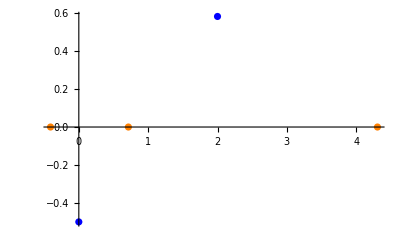

```mathematica
pkt=ListPlot[{sol,extr},PlotStyle->{{Orange,Large},{Blue,Large}}]
```

```mathematica
Limit[f[x],x->∞]
```

-1/2

```mathematica
as=Limit[f[x],x->∞]
```

-1/2

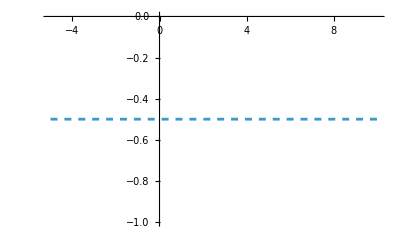

```mathematica
asy=Plot[as,{x,-5,10},PlotStyle->Dashed]
```

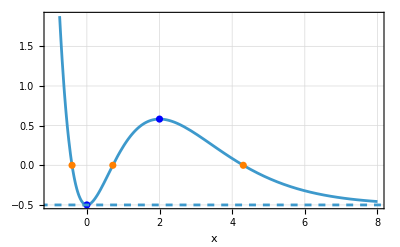

```mathematica
Show[wykres,pkt,asy]
```

# Zad 2

π^4/90

1.082

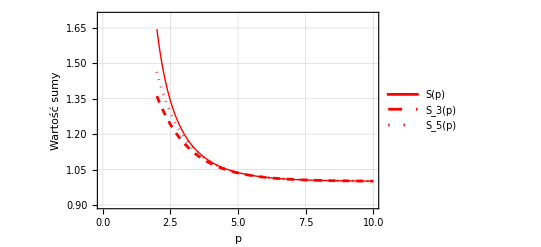

22

7

```mathematica
S[p_]:=Sum[1/n^p,{n,1,Infinity}]
Sk[p_,k_]:=Sum[1/n^p,{n,1,k}]

(*Podpunkt 1:Oblicz S(4) i podaj przybliżenie numeryczne*)
s4exact=S[4]
s4approx=N[s4exact,4]
plot2=Plot[{S[p],Sk[p,3],Sk[p,5]},{p,2,10},PlotStyle->{{Red,Thick},{Red,Dashed},{Red,Dotted}},PlotRange->{{0,10},{0.9,1.7}},Frame->True,GridLines->Automatic,FrameLabel->{"p","Wartość sumy"},PlotLegends->{"S(p)","S_3(p)","S_5(p)"}]


kmin[p_]:=SelectFirst[Range[1,1000],Abs[S[p]-Sk[p,#]]<10^-3&]

kod3=kmin[3]
kod4=kmin[4]
```

# Zad 3 full

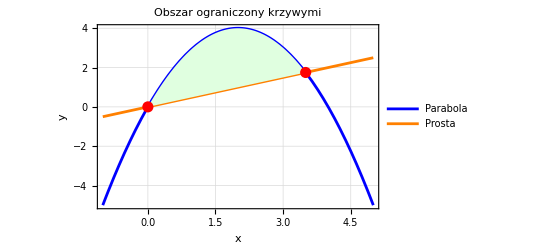

Pole powierzchni: 343/48

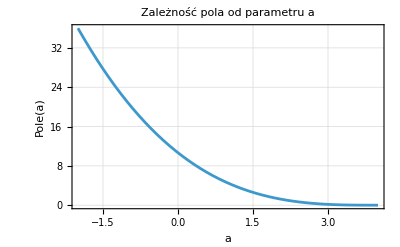

```mathematica
y1[x_]:=-x^2+4x
y2[x_,a_]:=a*x

aVal=1/2;

(*Podpunkt 2:Znajdowanie punktów przecięcia*)
rozwiazanie=Solve[y1[x]==y2[x,aVal],x];
xPunkty=x/. rozwiazanie; (*Pobranie samych wartości x*)
xMin=Min[xPunkty];        (*Dolna granica całki/cieniowania*)
xMax=Max[xPunkty];        (*Górna granica całki/cieniowania*)

punktyNaWykres={x,y1[x]}/. rozwiazanie;

(*---RYSOWANIE Z OGRANICZONYM CIENIOWANIEM---*)

(*Krok A:Rysujemy same krzywe w szerokim zakresie[-1,5]*)
wykresLinie=Plot[{y1[x],y2[x,aVal]},{x,-1,5},PlotStyle->{Blue,Orange},Frame->True,GridLines->Automatic,FrameLabel->{"x","y"},PlotLegends->{"Parabola","Prosta"}];

(*Krok B:Rysujemy wypełnienie TYLKO w zakresie przecięcia[xMin,xMax]*)
wykresWypelnienie=Plot[{y1[x],y2[x,aVal]},{x,xMin,xMax},PlotStyle->None,(*Nie rysuj linii ponownie,tylko wypełnienie*)Filling->{1->{2}},FillingStyle->LightGreen (*Kolor cieniowania*)];

(*Krok C:Rysujemy punkty przecięcia*)
wykresPunkty=ListPlot[punktyNaWykres,PlotStyle->{Red,PointSize[0.02]}];

(*Krok D:Łączymy wszystko w jedną całość*)
Show[wykresLinie,wykresWypelnienie,wykresPunkty,PlotLabel->"Obszar ograniczony krzywymi"]


(*Podpunkt 3:Obliczanie pola*)
pole=Integrate[y1[x]-y2[x,aVal],{x,xMin,xMax}];
Print["Pole powierzchni: ",pole]


(*Podpunkt 4: Zależność pola od parametru a*)
(*Obliczamy granice przecięcia symbolicznie dla parametru'a'*) 
xSolA=x/. Solve[y1[x]==y2[x,a],x];
(*Zakładamy,że pierwiastki to 0 i (4-a)*)
limit1=xSolA[[1]];
limit2=xSolA[[2]];
(*Wzór na pole*)
poleOdA[a_]=Integrate[y1[x]-y2[x,a],{x,limit1,limit2}];
(*Wykres pola od parametru a*) 
Plot[poleOdA[a],{a,-2,4},Frame->True,GridLines->Automatic,FrameLabel->{"a","Pole(a)"},PlotLabel->"Zależność pola od parametru a"]
```